```mathematica
ref[L_]:=Reverse[L];
rot[L_]:=ref[Transpose[L]];
```

```mathematica
sym[L_]:=Union[{L,rot[L],rot[
    rot[L]],rot[rot[rot[L]]]}]
```

```mathematica
digits={{{1,1,1,1,1}},{{2,2,2,0,2},{2,0,2,0,2},{2,0,2,2,2}},{{3,3,3,3,3},{3,0,3,0,3},{3,0,3,0,3}},{{4,4,4,4,4},{0,0,4,0,0},{4,4,4,0,0}},
{{5,0,5,5,5},{5,0,5,0,5},{5,5,5,0,5}},
{{0,0,6,6,6},{0,0,6,0,6},{6,6,6,6,6}},{{7,7,7,7,7},{7,0,0,0,0},{7,0,0,0,0}},{{8,8,8,8,8},{8,0,8,0,8},{8,8,8,8,8}},{{9,9,9,9,9},{9,0,9,0,9},{9,9,9,0,9}}};
```

```mathematica
alldigits=Flatten[Map[sym,digits],1];
```

```mathematica
addUD[poly_,a_,b_]:=Module[{i},
len=Length[poly[[1]]];p=poly;
For[i=1,i≤a,i++,p=Join[{Table[0,{len}]},p]];
For[i=1,i≤b,i++,p=Join[p,{Table[0,{len}]}]];p]
```

```mathematica
addLR[poly_,a_,b_]:=Transpose[addUD[Transpose[poly],a,b]]
```

```mathematica
translate[poly_]:=Module[{i,j,dp1,dp2},
{dp1,dp2}=Dimensions[poly];
Flatten[Table[addUD[addLR[poly,i,size-dp2-i],j,size-dp1-j],{i,0,size-dp2},{j,0,size-dp1}],1]]
```

```mathematica
col={Hue[0],Hue[.55],Hue[.17],Hue[.35],Hue[.1],RGBColor[0,.5,0],RGBColor[.5,.5,1],RGBColor[0,1,1],RGBColor[1,.5,1]};
```

```mathematica
ransub[L_,n_]:=Module[{num,sub,r},num=Length[L];If[num==n,Return[L]];sub={};While[Length[sub]<n,r=RandomInteger[{1,num}];sub=sub∪{L⟦r⟧}];sub]
```

```mathematica
pic[L1_,A_]:=Module[{},d1=Length[L1];d2=Length[L1⟦1⟧];Print[Style[Show[Graphics[{Table[If[MemberQ[A,{ii,jj}],{GrayLevel[0.5],Rectangle[{ii-0.75,jj-0.75},{ii-0.25,jj-0.25}]},{}],{ii,1,d1},{jj,1,d2}],GrayLevel[0],Line[{{0,0},{0,d2},{d1,d2},{d1,0},{0,0}}]}],AspectRatio->Automatic,ImageSize->20 (d1+0.2),PlotRange->{{-0.1,d1+0.1},{-0.1,d2+0.1}}],Antialiasing->False]];Print[Style[Show[Graphics[{AbsoluteThickness[2],Table[If[L1⟦ii,jj⟧>0,{col⟦Floor[L1⟦ii,jj⟧]⟧,Rectangle[{ii-1,jj-1},{ii,jj}]},{}],{ii,1,d1},{jj,1,d2}],Table[If[L1⟦ii,jj⟧=!=L1⟦ii+1,jj⟧,Line[{{ii,jj-1},{ii,jj}}],{}],{ii,1,d1-1},{jj,1,d2}],Table[If[L1⟦ii,jj⟧=!=L1⟦ii,jj+1⟧,Line[{{ii-1,jj},{ii,jj}}],{}],{ii,1,d1},{jj,1,d2-1}],Table[If[MemberQ[A,{ii,jj}],{GrayLevel[0.5],Rectangle[{ii-0.75,jj-0.75},{ii-0.25,jj-0.25}]},{}],{ii,1,d1},{jj,1,d2}],Line[{{0,0},{0,d2},{d1,d2},{d1,0},{0,0}}]}],AspectRatio->Automatic,ImageSize->20 (d1+0.2),PlotRange->{{-0.1,d1+0.1},{-0.1,d2+0.1}}],Antialiasing->False]]]
```

```mathematica
g[i_]:=Count[B,_?(i[[Apply[Sequence,#]]]>0&)]==Floor[Max[i]]
```

```mathematica
chec[ind_]:=Apply[And,Map[g,ind]]
```

```mathematica
generate:=Module[{},circs=0;While[circs<0.1 size^2||used<0.6 size^2,A=Table[0,{size},{size}];ind={};For[i=1,i≤5000,i++,r=RandomInteger[{1,Length[allalldigits]}];poly=(1+RandomReal[]/9) allalldigits⟦r⟧;value=Floor[Max[poly]];If[(Position[A,_?(#1>0&)])∩(Position[poly,_?(#1>0&)])=={}&&((Abs[value-4]=!=3&&(Abs[value-7/2]==3/2||RandomReal[]>0.8))||i>4000),A=A+poly;AppendTo[ind,poly]]];circs=Total[(Floor[Max[#1]]&)/@ind];used=Count[Flatten[A],_?Positive]];B=Flatten[(ransub[Position[#1,_?(#1>0&)],Floor[Max[#1]]]&)/@ind,1]]
```

```mathematica
uniq[B_]:=Module[{},
ct=0;
aad=Select[allalldigits,chec[{#}]&];
ddd=Map[Position[#,_?(#>0&)]&,aad];
stac={{}};
While[Length[stac]>0,
top=First[stac];
stac=Rest[stac];
com=Complement[B,top];
If[com=!={},
pos=First[com];
nex=Select[ddd,MemberQ[#,pos]&&Intersection[top,#]=={}&];
m=Map[Union[top,#]&,nex];
mmm=Map[Complement[B,#]&,m];
ct=ct+Count[mmm,{}];
If[ct>1,Return[False]];
stac=Join[m,stac]
]];
ct==1
]
```

```mathematica
size=12;
allalldigits=Flatten[Map[translate,alldigits],1];
```

```mathematica
While[0==0,
z=False;
While[Not[z],
generate;
z=uniq[B]];
pic[A,B];]
```

## 12x12

## 10x10

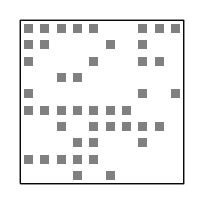

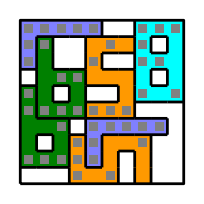

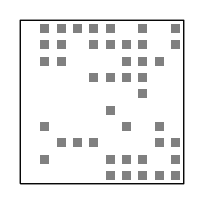

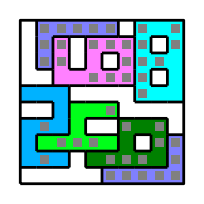

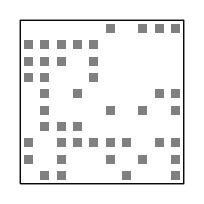

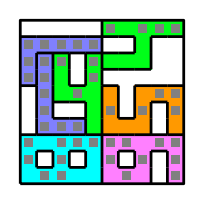

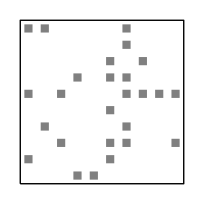

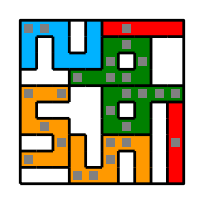

## 9x9

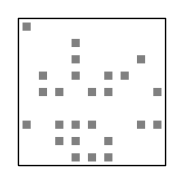

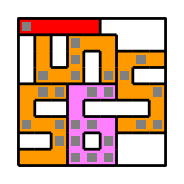

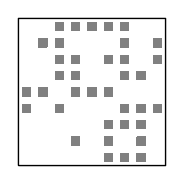

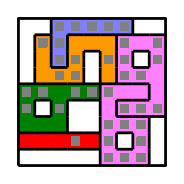

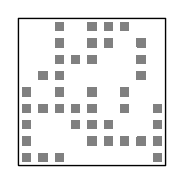

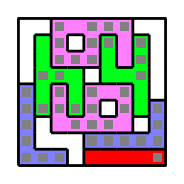

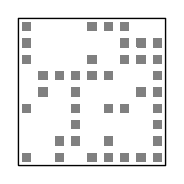

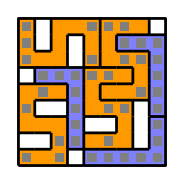

## 8x8

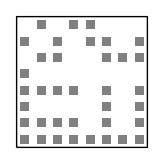

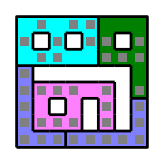

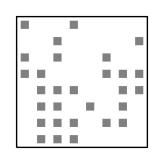

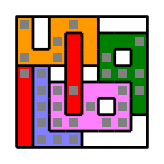

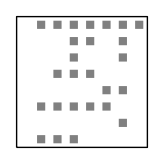

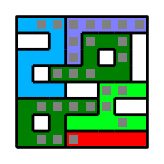

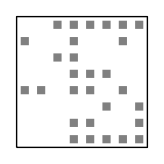

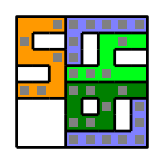

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»